```mathematica
weights = {26,54,26,47,44,90,92,93,8,27,97,14,75,22,28,36,41,44,56,21,36,56,49,59}
```

{26,54,26,47,44,90,92,93,8,27,97,14,75,22,28,36,41,44,56,21,36,56,49,59}

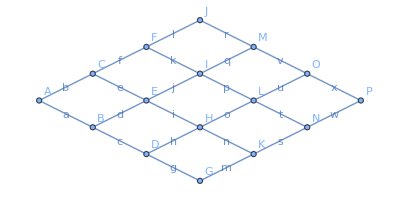

```mathematica
shortestPathGraph=EdgeTaggedGraph[
CharacterRange["A","P"],
{
"A"<->"B","A"<->"C",
"B"<->"D","B"<->"E",
"C"<->"E","C"<->"F",
"D"<->"G","D"<->"H",
"E"<->"H","E"<->"I",
"F"<->"I","F"<->"J",
"G"<->"K",
"H"<->"K","H"<->"L",
"I"<->"L", "I"<->"M",
"J"<->"M",
"K"<->"N",
"L"<->"N", "L"<->"O",
"M"<->"O",
"N"<->"P",
"O"<->"P"
}->CharacterRange["a","x"],
EdgeWeight->weights,
VertexLabels->"Name",
EdgeLabels->"EdgeTag",
GraphLayout->{"SymmetricLayeredEmbedding","Rotation"->90 Degree}
]
```

```mathematica
shortestPathGraph
```

-Graphics-

```mathematica
dists =GraphDistanceMatrix[shortestPathGraph, Method -> "Dijkstra"]
```

{{0.,26.,54.,52.,73.,144.,144.,81.,100.,158.,103.,109.,141.,130.,145.,179.},{26.,0.,80.,26.,47.,170.,118.,55.,74.,159.,77.,83.,115.,104.,119.,153.},{54.,80.,0.,106.,44.,90.,149.,52.,71.,104.,74.,80.,112.,101.,116.,150.},{52.,26.,106.,0.,73.,196.,92.,81.,100.,185.,103.,109.,141.,130.,145.,179.},{73.,47.,44.,73.,0.,124.,105.,8.,27.,112.,30.,36.,68.,57.,72.,106.},{144.,170.,90.,196.,124.,0.,229.,132.,97.,14.,154.,133.,58.,154.,114.,173.},{144.,118.,149.,92.,105.,229.,0.,97.,132.,217.,75.,125.,173.,131.,161.,180.},{81.,55.,52.,81.,8.,132.,97.,0.,35.,120.,22.,28.,76.,49.,64.,98.},{100.,74.,71.,100.,27.,97.,132.,35.,0.,85.,57.,36.,41.,57.,72.,106.},{158.,159.,104.,185.,112.,14.,217.,120.,85.,0.,142.,121.,44.,142.,100.,159.},{103.,77.,74.,103.,30.,154.,75.,22.,57.,142.,0.,50.,98.,56.,86.,105.},{109.,83.,80.,109.,36.,133.,125.,28.,36.,121.,50.,0.,77.,21.,36.,70.},{141.,115.,112.,141.,68.,58.,173.,76.,41.,44.,98.,77.,0.,98.,56.,115.},{130.,104.,101.,130.,57.,154.,131.,49.,57.,142.,56.,21.,98.,0.,57.,49.},{145.,119.,116.,145.,72.,114.,161.,64.,72.,100.,86.,36.,56.,57.,0.,59.},{179.,153.,150.,179.,106.,173.,180.,98.,106.,159.,105.,70.,115.,49.,59.,0.}}

```mathematica
dists[[1]]
```

{0.,26.,54.,52.,73.,144.,144.,81.,100.,158.,103.,109.,141.,130.,145.,179.}

```mathematica
times = AssociationThread[CharacterRange["A", "P"], dists[[1]]]
```

<|A→0.,B→26.,C→54.,D→52.,E→73.,F→144.,G→144.,H→81.,I→100.,J→158.,K→103.,L→109.,M→141.,N→130.,O→145.,P→179.|>

```mathematica
annotatedGraph = VertexReplace[shortestPathGraph, times]
```

VertexReplace::reps: <|A→0.,B→26.,C→54.,D→52.,E→73.,F→144.,G→144.,H→81.,I→100.,J→158.,K→103.,L→109.,M→141.,N→130.,O→145.,P→179.|> is not a list of replacement rules.

VertexReplace[-Graphics-,<|A→0.,B→26.,C→54.,D→52.,E→73.,F→144.,G→144.,H→81.,I→100.,J→158.,K→103.,L→109.,M→141.,N→130.,O→145.,P→179.|>]

```mathematica
dists//MatrixForm
```

(0. | 26. | 54. | 52. | 73. | 144. | 144. | 81. | 100. | 158. | 103. | 109. | 141. | 130. | 145. | 179.
26. | 0. | 80. | 26. | 47. | 170. | 118. | 55. | 74. | 159. | 77. | 83. | 115. | 104. | 119. | 153.
54. | 80. | 0. | 106. | 44. | 90. | 149. | 52. | 71. | 104. | 74. | 80. | 112. | 101. | 116. | 150.
52. | 26. | 106. | 0. | 73. | 196. | 92. | 81. | 100. | 185. | 103. | 109. | 141. | 130. | 145. | 179.
73. | 47. | 44. | 73. | 0. | 124. | 105. | 8. | 27. | 112. | 30. | 36. | 68. | 57. | 72. | 106.
144. | 170. | 90. | 196. | 124. | 0. | 229. | 132. | 97. | 14. | 154. | 133. | 58. | 154. | 114. | 173.
144. | 118. | 149. | 92. | 105. | 229. | 0. | 97. | 132. | 217. | 75. | 125. | 173. | 131. | 161. | 180.
81. | 55. | 52. | 81. | 8. | 132. | 97. | 0. | 35. | 120. | 22. | 28. | 76. | 49. | 64. | 98.
100. | 74. | 71. | 100. | 27. | 97. | 132. | 35. | 0. | 85. | 57. | 36. | 41. | 57. | 72. | 106.
158. | 159. | 104. | 185. | 112. | 14. | 217. | 120. | 85. | 0. | 142. | 121. | 44. | 142. | 100. | 159.
103. | 77. | 74. | 103. | 30. | 154. | 75. | 22. | 57. | 142. | 0. | 50. | 98. | 56. | 86. | 105.
109. | 83. | 80. | 109. | 36. | 133. | 125. | 28. | 36. | 121. | 50. | 0. | 77. | 21. | 36. | 70.
141. | 115. | 112. | 141. | 68. | 58. | 173. | 76. | 41. | 44. | 98. | 77. | 0. | 98. | 56. | 115.
130. | 104. | 101. | 130. | 57. | 154. | 131. | 49. | 57. | 142. | 56. | 21. | 98. | 0. | 57. | 49.
145. | 119. | 116. | 145. | 72. | 114. | 161. | 64. | 72. | 100. | 86. | 36. | 56. | 57. | 0. | 59.
179. | 153. | 150. | 179. | 106. | 173. | 180. | 98. | 106. | 159. | 105. | 70. | 115. | 49. | 59. | 0.)